Solution of 3d Apollonius problem

```mathematica
ApolloniusSolution[T_,S_]:=Module[
{M,b,AugM,Mrr,Sr},
Subscript[x, 1]=T[[1,1]]; Subscript[y, 1]=T[[1,2]]; Subscript[z, 1]=T[[1,3]]; Subscript[r, 1]=ρ a;
Subscript[x, 2]=T[[2,1]]; Subscript[y, 2]=T[[2,2]]; Subscript[z, 2]=T[[2,3]]; Subscript[r, 2]=ρ a;
Subscript[x, 3]=T[[3,1]]; Subscript[y, 3]=T[[3,2]]; Subscript[z, 3]=T[[3,3]]; Subscript[r, 3]=ρ a;
Subscript[x, 4]=T[[4,1]]; Subscript[y, 4]=T[[4,2]]; Subscript[z, 4]=T[[4,3]]; Subscript[r, 4]=ρ a;
Subscript[s, 1]=S[[1]]; Subscript[s, 2]=S[[2]]; Subscript[s, 3]=S[[3]]; Subscript[s, 4]=S[[4]];

M={{-2(Subscript[x, 1]-Subscript[x, 2]),-2(Subscript[y, 1]-Subscript[y, 2]),-2(Subscript[z, 1]-Subscript[z, 2]),-2(Subscript[s, 1] Subscript[r, 1]-Subscript[s, 2] Subscript[r, 2])},{-2(Subscript[x, 1]-Subscript[x, 3]),-2(Subscript[y, 1]-Subscript[y, 3]),-2(Subscript[z, 1]-Subscript[z, 3]),-2(Subscript[s, 1] Subscript[r, 1]-Subscript[s, 3] Subscript[r, 3])},{-2(Subscript[x, 1]-Subscript[x, 4]),-2(Subscript[y, 1]-Subscript[y, 4]),-2(Subscript[z, 1]-Subscript[z, 4]),-2(Subscript[s, 1] Subscript[r, 1]-Subscript[s, 4] Subscript[r, 4])}};
b={{Subscript[x, 2]^2-Subscript[x, 1]^2+Subscript[y, 2]^2-Subscript[y, 1]^2+Subscript[z, 2]^2-Subscript[z, 1]^2+Subscript[r, 1]^2-Subscript[r, 2]^2},{Subscript[x, 3]^2-Subscript[x, 1]^2+Subscript[y, 3]^2-Subscript[y, 1]^2+Subscript[z, 3]^2-Subscript[z, 1]^2+Subscript[r, 1]^2-Subscript[r, 3]^2},{Subscript[x, 4]^2-Subscript[x, 1]^2+Subscript[y, 4]^2-Subscript[y, 1]^2+Subscript[z, 4]^2-Subscript[z, 1]^2+Subscript[r, 1]^2-Subscript[r, 4]^2}};

AugM=Transpose[Append[Transpose[M],Flatten[b]]];
Mrr=RowReduce[AugM];

Subscript[x, s]=Mrr[[1,5]]-r*Mrr[[1,4]];
Subscript[y, s]=Mrr[[2,5]]-r*Mrr[[2,4]];
Subscript[z, s]=Mrr[[3,5]]-r*Mrr[[3,4]];

Sr =Solve[(Subscript[x, s]-Subscript[x, 1])^2 + (Subscript[y, s]-Subscript[y, 1])^2 +(Subscript[z, s]-Subscript[z, 1])^2==(r+Subscript[s, 1] Subscript[r, 1])^2,r];
r/.Sr
]
```

```mathematica
p={a{0,0,0},a{1,0,0},a{1/2,Sqrt[3]/2,0},a{1/2,1/(2 Sqrt[3]), Sqrt[2/3]},a{3/2,Sqrt[3]/2,0}};
Subscript[T, 1]=p[[{1,2,3,4}]];
Subscript[T, 2]=p[[{2,3,4,5}]];
Sall=Tuples[{-1,1},4];
```

### Tetrahedron 1

```mathematica
AllResults = Flatten[Map[ApolloniusSolution[Subscript[T, 1],#]&,Sall]];
ResultsPositive = Select[AllResults,Positive[Re[#/.{a->1,ρ->0.001}]]&];
Results =FullSimplify[DeleteDuplicates[ResultsPositive]]
```

{1/4 a (√6+4 ρ),(2 a ρ+√6 √(a^2 (-1+4 ρ^2)^2))/(4-24 ρ^2),(a √(-3+8 ρ^2))/(2 √(-2+16 ρ^2)),(2 a ρ-√6 √(a^2 (-1+4 ρ^2)^2))/(-4+24 ρ^2),1/4 a (√6-4 ρ)}

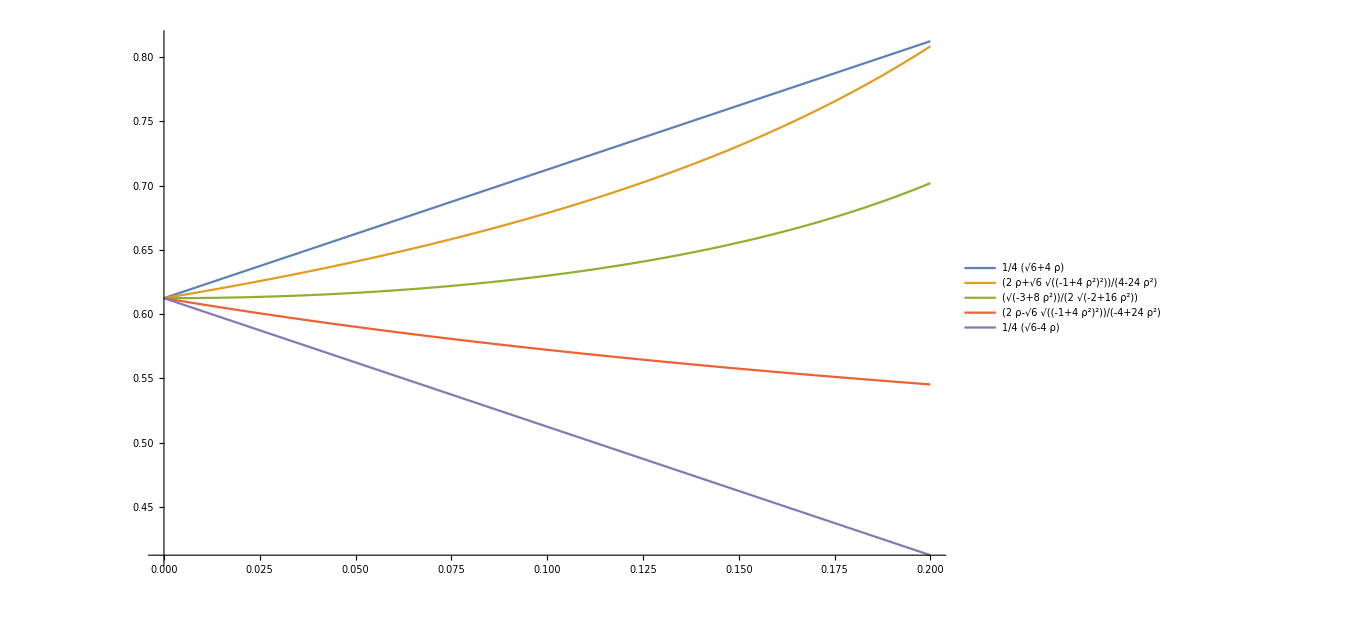

```mathematica
Show[Plot[Evaluate[Results/.a->1],{ρ,0,0.2},PlotLegends->"Expressions",LabelStyle->Directive[Black,23], PlotRange->Full],ImageSize->1000]
```

### Tetrahedron 2

```mathematica
AllResults = Flatten[Map[ApolloniusSolution[Subscript[T, 2],#]&,Sall]];
ResultsPositive = Select[AllResults,Positive[Re[#/.{a->1,ρ->0.001}]]&];
Results =FullSimplify[DeleteDuplicates[ResultsPositive]]
```

{a (1/(√2)+ρ),(a √(-1+2 ρ^2))/(√(-2+12 ρ^2)),(2 a ρ-√2 √(a^2 (1-16 ρ^2+32 ρ^4)))/(-2+32 ρ^2),(2 a ρ+√2 √(a^2 (-1+4 ρ^2)^2))/(2-16 ρ^2),(2 a ρ-√2 √(a^2 (-1+4 ρ^2)^2))/(-2+16 ρ^2),(2 a ρ+√2 √(a^2 (1-16 ρ^2+32 ρ^4)))/(2-32 ρ^2),a (1/(√2)-ρ)}

```mathematica
Show[Plot[Evaluate[Results/.a->1],{ρ,0,0.2},PlotLegends->"Expressions",LabelStyle->Directive[Black,23], PlotRange->Full],ImageSize->1000]
```